## Using Mathematica for probability

In this notebook, we will provide the input cells for the examples -- you should evaluate each input cell to see the outputs. In some cases, later examples may not work if you haven’t evaluated all the previous input cells, so please evaluate each example.

### Working with probability distributions

Mathematica knows about a lot of families of probability distributions. One of the simplest is the discrete uniform distribution. For example, DiscreteUniformDistribution[{1,10}] represents the uniform distribution on the integers from 1 to 10 -- the distribution under which all those integers are equally likely to be chosen.

```mathematica
DiscreteUniformDistribution[{1,10}]
```

DiscreteUniformDistribution[{1,10}]

As you can see, it evaluates to itself -- there is no way to simplify or reduce it. It doesn’t do anything until you pass it in to another function, such as RandomVariate. RandomVariate  samples from a distribution, as in

```mathematica
RandomVariate[DiscreteUniformDistribution[{1,10}]]
```

4

This in essence “simulates” a process that follows the distribution you pass in. You can give the number of samples you want as a second argument:

```mathematica
RandomVariate[DiscreteUniformDistribution[{1,10}],5]
```

{10,7,7,7,1}

```mathematica
RandomInteger[{1,10},5]
```

{8,5,8,2,1}

RandomVariate gets more interesting and useful when the distribution isn't uniform. For example, EmpiricalDistribution allows you to specify the probability of each outcome explicitly, as in

```mathematica
eDist=EmpiricalDistribution[{.2,.6,.1,.1}->{1,2,3,4}]
```

DataDistribution[…]

Now if we sample from it, we’ll get a lot more 2’s than anything else, then 1’s, and occasional 3’s and 4’s.

```mathematica
data=RandomVariate[eDist,100]
```

{3,4,4,1,2,3,1,2,2,2,2,2,4,2,2,2,2,3,2,3,2,2,2,2,2,2,2,2,2,4,2,2,1,4,1,2,2,2,4,2,1,2,3,2,2,2,3,2,4,2,1,1,1,2,2,1,1,2,2,1,2,2,4,2,1,3,2,1,2,2,2,2,2,2,1,4,2,4,2,2,2,2,3,2,2,1,1,2,2,2,2,3,2,2,1,3,1,4,2,1}

You can also just pass in a list and it will use the frequencies from the list to generate an empirical distribution:

```mathematica
eDist2=EmpiricalDistribution[data]
```

DataDistribution[…]

Here’s an example of sampling approximate reals from a continuous distribution -- the normal (Gaussian) distribution with mean 5 and standard deviation 2:

```mathematica
RandomVariate[NormalDistribution[5, 2], 20]
```

{5.7018,6.21255,6.62816,7.06752,3.73147,3.67475,5.50937,2.36826,5.72456,6.37674,4.03477,2.88624,4.75445,0.835376,5.48594,5.04261,7.74179,1.82004,2.01913,1.53921}

We can plot a histogram of a larger sample to see the familiar “bell curve” shape:

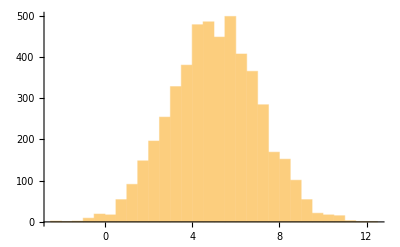

```mathematica
Histogram[RandomVariate[NormalDistribution[5, 2], 5000]]
```

That was a plot of a sample, but we can also plot the distribution itself:

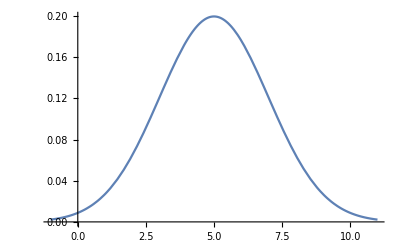

```mathematica
Plot[PDF[NormalDistribution[5, 2], x],{x, -1, 11}]
```

The function PDF (for “probability density function”) gives the probability density at a particular point. For example,

```mathematica
PDF[NormalDistribution[5, 2], 7]
```

1/(2 √(2 ⅇ π))

This gives the probability density at 7 as an exact real. To get an approximate decimal, use N:

```mathematica
N[PDF[NormalDistribution[5, 2], 7]]
```

0.120985

The second argument to Plot, {x, -1, 11}, indicates that the x in the first argument should be varied from -1 to 11.

##### Practice: Plotting samples and probability distributions

Use RandomVariate with BinomialDistribution to simulate the number of heads produced in 10 tosses of a coin with probability 0.8 of producing a heads on each flip (called a success). This won’t give the outcomes of individual flips -- each sample from this binomial distribution will give the total number of heads in 10 flips.

```mathematica
RandomVariate[BinomialDistribution[10,.8]]
```

7

Plot a histogram of the numbers of heads produced in 1,000 such experiments.

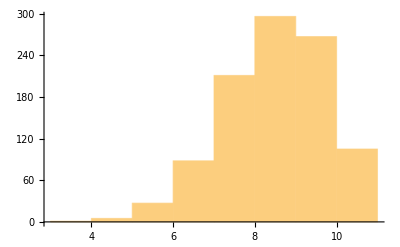

```mathematica
Histogram[RandomVariate[BinomialDistribution[10,.8],1000]]
```

Plot the actual probability function of the binomial distribution with these parameters, from 0 to 10. The only values with non-zero probability are the integers from 0 to 10, so will want to use DiscretePlot instead of Plot for this. Inside of DiscretePlot you will use PDF and BinomialDistribution. (deGroot uses the term probability function instead of p.d.f. for discrete random variates, but Mathematica allows you to use PDF for both.)

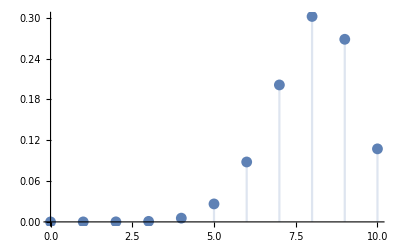

```mathematica
DiscretePlot[
PDF[
BinomialDistribution[10,.8],
x
],{x,0,10}
]
```

#### Calculating the probabilities of events

When working with probability distributions, often you will want to know the cumulative distribution function (CDF) rather than the probability density function (PDF). For a discrete random variable, the CDF evaluated at some number x is the sum of the probabilities of all numbers less than or equal to x. For a continuous random variable, it is the integral of the PDF from -∞ to x. Mathematica will provide CDF for any distribution it knows:

```mathematica
N[CDF[NormalDistribution[5, 2], 7]]
```

0.841345

This is the probability of selecting a number less than or equal 7 from the specified distribution. Notice how different it is than the PDF of the same distribution evaluated at 7. We can also plot the CDF, which always ranges from 0 to 1:

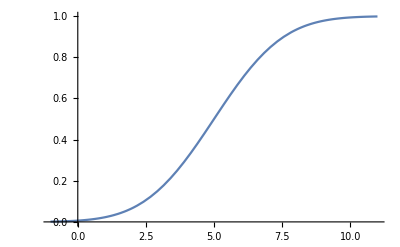

```mathematica
Plot[CDF[NormalDistribution[5, 2], x],{x, -1, 11}]
```

Compare this to the PDF we graphed for the same function above. You can see that the CDF rises steeply where the PDF is high and slowly where the PDF is low. This is because the PDF is the derivative of the CDF.

##### Practice: Cumulative Probability Distributions

Use DiscretePlot and CDF to plot the cumulative distribution function of the binomial distribution for 10 tosses of a coin with probability 0.8 of producing a heads. Compare to your plot of the pdf for the same distribution. To make the y-axes comparable, you may want to add the following option to DiscretePlot: PlotRange -> {0, 1}. Optional arguments to a function go after all the other arguments, each separated from the others by a comma. See documentation on Plot for examples.

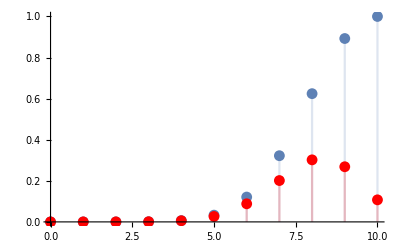

```mathematica
Show[DiscretePlot[CDF[BinomialDistribution[10,0.8],x],{x,0,10}],DiscretePlot[PDF[BinomialDistribution[10,0.8],x],{x,0,10},PlotStyle->Red]]
```

Now plot the CDF for the tosses of a coin with probability 0.7 of producing heads. Now try 0.6. Write a comment on what happens as you decrease the probability of heads. To make the graphs comparable, you may want to add the following option to DiscretePlot: PlotRange -> {0, 1}.

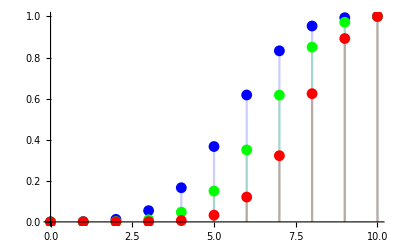

```mathematica
Show[
DiscretePlot[CDF[BinomialDistribution[10,0.6],x],{x,0,10},PlotStyle->Blue],
DiscretePlot[CDF[BinomialDistribution[10,0.7],x],{x,0,10},PlotStyle->Green],DiscretePlot[CDF[BinomialDistribution[10,0.8],x],{x,0,10},PlotStyle->Red]]
```

```mathematica
(* As the probablity of a heads decreases, the CDF shifts left. *)
```

You can use the CDF to calculate the probability of a number sampled from the distribution falling in a certain interval. For example, the probability of a number being between 3 and 7 is simply the probability of its being below 7 minus the probability of its being below 3. That is, the value of the CDF at 7 minus the value of the CDF at 3.

```mathematica
N[CDF[NormalDistribution[5, 2], 7]] - N[CDF[NormalDistribution[5, 2], 3]]
```

0.682689

But you don’t actually have to subtract the CDF values explicitly -- Mathematica does this and much more with the function Probability.

```mathematica
N[Probability[z<7,z \[Distributed] NormalDistribution[5, 2]]]
```

0.841345

```mathematica
N[Probability[3<z<7,z \[Distributed] NormalDistribution[5, 2]]]
```

0.682689

Notice that these are the same numbers we got by using CDF. The first argument to Probability is a predicate -- something that evaluates to True or False -- involving an undefined variable. The second argument gives the distribution of that variable. The little squiggle, \[Distributed], is read “is distributed according to” and can be obtained by typing the escape key, “dist”, and escape again. What’s cool about Probability is that you can give it complicated predicates, as in

```mathematica
N[Probability[2<Sqrt[z] && z^3<125,z \[Distributed] NormalDistribution[5, 2]]]
```

0.191462

This gives the probability of selecting a number whose square root is greater than two and whose cube is less than 125. By using && (and) and || (or) you can make very complex predicates to calculate the probability of. One thing to beware of is that if you try this with a variable that has a defined value Mathematica will simply replace it by its value before evaluating the rest of the expression. This doesn’t do what you want -- it usually returns a probably of 1 or 0, depending on whether the value of the variable does or does not satisfy your predicate. So you want to make sure your variable is colored blue, indicating undefined, when you use Probability.

If you’re interested in getting out decimal numbers rather than big symbolic expressions, you can use the function NProbability, which in some cases may be faster than computing a symbolic expression for the probability first and then passing it to N.

##### Practice: Using Probability

Suppose you “flip a coin” that has probability 0.75 of producing heads 20 times and add up the number of heads actually produced. You then square that number. Use Probability to figure out the probability that the result will lie in the interval between 20 and 100, inclusive.

```mathematica
NProbability[20≤z^2≤100,z\[Distributed]BinomialDistribution[20,.75]]
```

0.013864